```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Man\Dropbox\Cooldown (MN)\Cryo2_2021_08

```mathematica
Remove["Global`*"]
```

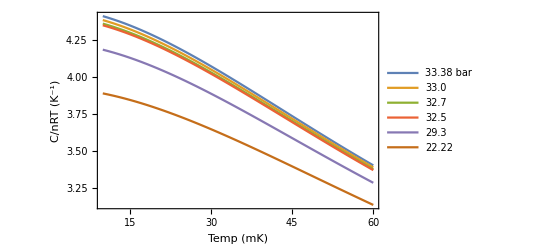

```mathematica
(*Greywall fit parameters for Cv for normal 3He in 1982 most accurate above 10mK. Has both temp and pressure dependence. For values near Tc, use the function coverNRT down below*)
a:={{-2.9190414,5.2893401 10^2,-1.8869641*10^4,2.6031315 10^5},{0,0,0,0},{-2.4752597*10^3,1.8377260 10^5,-3.4946553*10^6,0},{3.8887481 10^4,-2.8649769*10^6,5.2526785 10^7,0},{-1.7505655*10^5,1.2809001 10^7,-2.3037701*10^8,0}}(*Greywall fit parameters for cv for normal 3He in 1982*);
a//TableForm;
cvOvernR=Sum[a[[i,j+1]] v^-j(t/1000)^i,{i,1,5},{j,0,3}];(*plug in temp in mK*)
cvfunc[v_,t_]=cvOvernR;(*cfunc = C/(nR). To get Subscript[C, v], multiply cvfunc with nR. V is molar volume, approx 25 cc at 33 bar*)

vmolcoef={36.837231,
-1.11803474,
0.083421417,
-0.38859562*10^-2,
0.94759780 10^-4,
-.91253577*10^-6
};
vmol[p_]=Sum[vmolcoef[[i]] p^(i-1),{i,1,6}](*Molar volume as a function of pressure for 3He in cc/mol*);

cvtotMCT[t_]=0.6/vmol[mctp[t]] 8.3cvfunc[vmol[mctp[t]],t](* cc/(mol/ cc)* Gas constant * C/(n R)*) (*Total heat capcity of the MCT with 0.6 cc of 3He at any temperature(mK)*);

cvtot3He[t_,p_,m_]=m/vmol[p] 8.3cvfunc[vmol[p],t](*Total heat capcity of "m" cc of 3He at any pressure(bar) and temperature(mK)*);

Cnuclear[i_,t_]=3.22 10^-6 (i 8./68.03)^2/(t/1000)^2*24;(*Cu demag stage heat capacity in J/K, i is in amps, t is in mili-Kelvin, 24 moles of of Cu, PLUG IN TEMPERATURE IN mK BUT RESULT in K*)

CnuclearPR[i_,t_]=1418 10^-6 (i 8./78.5)^2/(t/1000)^2*0.62; (*Subscript[PrN, 5] demag stag heat capacity in J/K,.62 moles of PrNi5. PLUG IN TEMPERATURE IN mK BUT RESULT in K*)

covertfunc[v_,t_]=cvfunc[v,t]/(t/1000);(*CoverTfunc = C/(n R T), plug in temp in mK*)

(*For C/(n R T) near Tc, plug temp in mK*)
coverNRTCoef={
2.7840464
,0.69575243 10^-1
,-0.14738303 10^-2
,0.46143498 10^-4
,-0.53785385 10^-6};
coverNRT[p_]=Sum[coverNRTCoef[[i]] p^(i-1),{i,1,5}];
Plot[
{covertfunc[25.585876,t],
covertfunc[25.659899,t],
covertfunc[25.727308,t],
covertfunc[25.758962,t],
covertfunc[26.25639,t],
covertfunc[27.307138,t]
}
,{t,10,60},
PlotLegends->{"33.38 bar","33.0","32.7","32.5","29.3","22.22"},Frame->True,FrameLabel->{"Temp (mK)","C/nRT (K^-1)"},BaseStyle->FontSize->16]

(*Temperature of MCT as a function of pressure, t in mK*)
t[p_]=114317991.5969163-p 12703936.00274829+p^2 329599.8777748932+p^3 6564.519293273008-p^4 162.9787303705037-p^5 7.597125382774742-p^6 0.03480988929473872+p^7 0.005350437149420069+p^8 0.0001629438818107907-p^9(7.162156256935981 10^-7)-p^10(1.685160233572245 10^-7)-p^11(2.299748954196923 10^-9)+p^12(1.773051798056648 10^-10)-p^13(1.811893544821193 10^-12);

(*Pressure of MCT as a function of temperature, t in mK*)
poftcoef={
34.42408358347273,
-0.03259934548610183,
-0.001115246032059229,
7.645709225225787*10^-5,
-2.785218662138949*10^(-06),
6.472218490397762*10^(-08),
-1.008133623203505*10^(-09),
1.082315232679171*10^(-11),
-8.108442874599485*10^(-14),
4.228499626505295*10^(-16),
-1.504018879529928*10^(-18),
3.477974853038849*10^(-21),
-4.712126086557339*10^(-24),
2.837825319137452*10^(-27)
};
mctp[t_]=Sum[poftcoef[[i]]*t^(i-1),{i,1,14}];
```

```mathematica
CnuclearPR[3.5,5]*0.2/1000*1/(24*3600)
coverNRT[386/14.5]0.6*8.34*5/1000
```

1.03567×10^-8

0.104887

```mathematica
coverNRTCoef={
2.7840464
,0.69575243 10^-1
,-0.14738303 10^-2
,0.46143498 10^-4
,-0.53785385 10^-6};
coverNRT[p_]=Sum[coverNRTCoef[[i]] p^(i-1),{i,1,5}];

coverNRT[34]
covertfunc[vmol[34],1]
```

4.54073

3.83203

```mathematica
10./(20 10^-9)
```

5.×10^8

```mathematica
5.67 10^-8(0.001)*4^4
```

1.45152×10^-8

```mathematica
dat=Import["C:\\Users\\Man\\Dropbox\\Cooldown (MN)\\Cryo2_2021_08\\20210902mct.txt","Table"];
```

```mathematica
dat[[1]]
Length[dat]
```

{capacitance,pressure,temp,time}

73952

```mathematica
dat[[2;;,3]]=t[dat[[2;;,2]]];
dat[[2;;,4]]=dat[[2;;,4]]-dat[[2,4]];
```

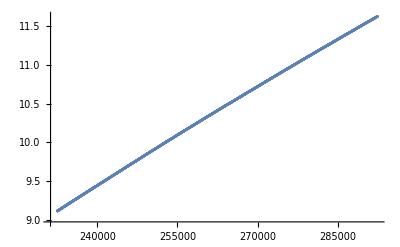

```mathematica
ListPlot[dat[[58000;;73000;;4,{4,3}]],PlotRange->All]
```

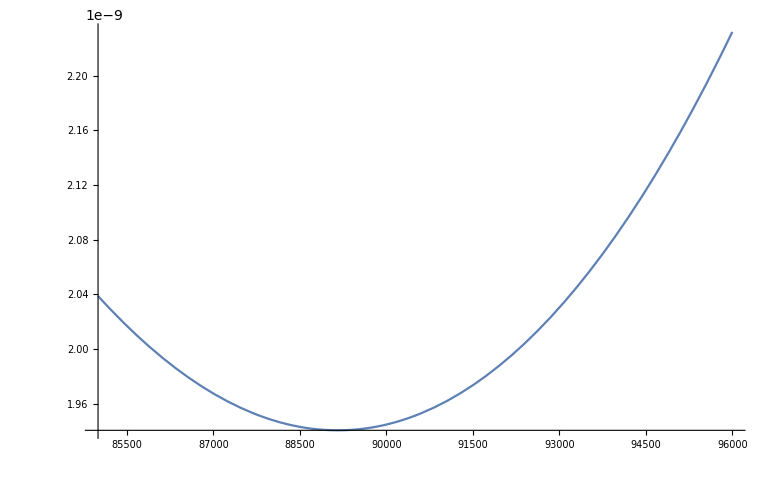

```mathematica
fdat[x_]=Fit[dat[[21000;;24000,{4,3}]],{1,x,x^2,x^3},x];
dfdat[x_]=D[fdat[x],x];
coverNRT[386/14.5038]*15/vmol[386/14.5038] 8.34*dfdat[x]/1000 fdat[x]/1000;
Plot[%,{x,85000,96000}]
```

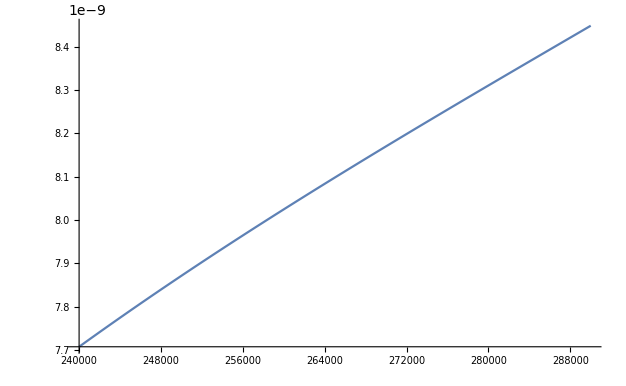

```mathematica
fdat[x_]=Fit[dat[[58000;;73000,{4,3}]],{1,x,x^2,x^3},x];
dfdat[x_]=D[fdat[x],x];
coverNRT[386/14.5038]*15/vmol[386/14.5038] 8.34*dfdat[x]/1000 fdat[x]/1000;
Plot[%,{x,240000,290000}]
```

```mathematica
vmol[386/14.5038]
```

28.2725

```mathematica
covertfunc[vmol[386/14.5038],4]
covertfunc[26.61,4]
```

3.69604

4.11726

```mathematica
cvtot3He[4,386/14.5,15](1 10^-6)/4
4.19*15/vmol[386/14.5]*8.34  4/1000*(0.5 10^-6)/4
```

1.62766×10^-8

9.27013×10^-9

```mathematica
15/vmol[386/14.5]
```

0.530562

```mathematica
NDSolve[{cvtot3He[temp[t],386/14.5,15]*temp'[t]/1000==1.5 10^-9,temp[0]==4.91},temp[t],t]
```

```mathematica
Clear[temp]
```

```mathematica
DSolve[{k*temp[t]temp'[t]==qdot,temp[0]==t0},temp[t],t]
```

{{temp[t]→-(√(2 qdot t+k t0^2))/(√k)},{temp[t]→(√(2 qdot t+k t0^2))/(√k)}}

```mathematica
(√2 √(qdot t+k C[1]))/(√k)
```

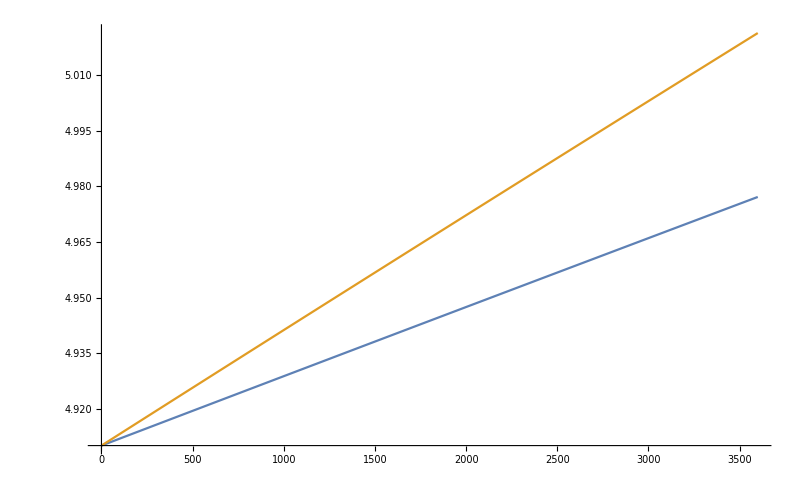

```mathematica
covert[t_]=cvtot3He[t,386/14.5,15]/t 1000;
Plot[{1000(√(2 1.5 10^-9 t+covert[5] (4.91/1000)^2))/(√covert[5]),1000(√(2 2.5 10^-9 t+covert[5] (4.91/1000)^2))/(√covert[5])},{t,0,3600}]
```

```mathematica
dat0=Import["20210828mct.txt","Table"];
```

```mathematica
dat0[[1]]
```

{capacitance,pressure,temp,time}

```mathematica
dat1=dat0[[2;;,{4,3}]];
dat1[[All,1]]=dat1[[All,1]]-dat1[[1,1]];
```

```mathematica
Length[dat1]
```

37841

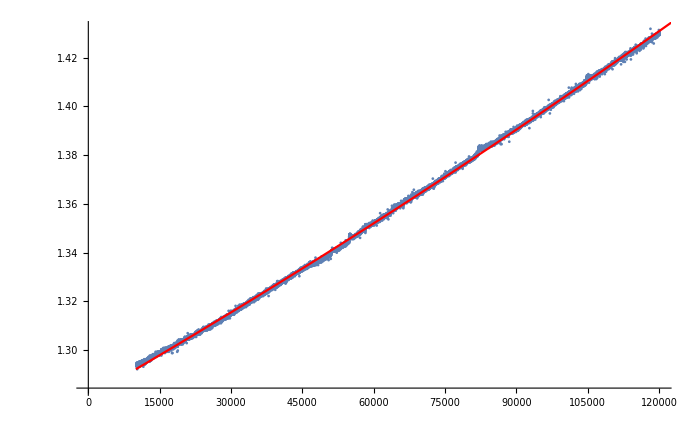

```mathematica
fdat=Fit[dat1[[2500;;30000]],{1,x,x^2},x];
Show[{
ListPlot[dat1[[2500;;30000]]]
,Plot[fdat,{x,10000,130000},PlotStyle->Red]
}]
```

```mathematica
tdot[x_]=D[fdat,x]
fdat
```

1.12198×10^-6+2.12785×10^-12 x

1.28085+1.12198×10^-6 x+1.06392×10^-12 x^2

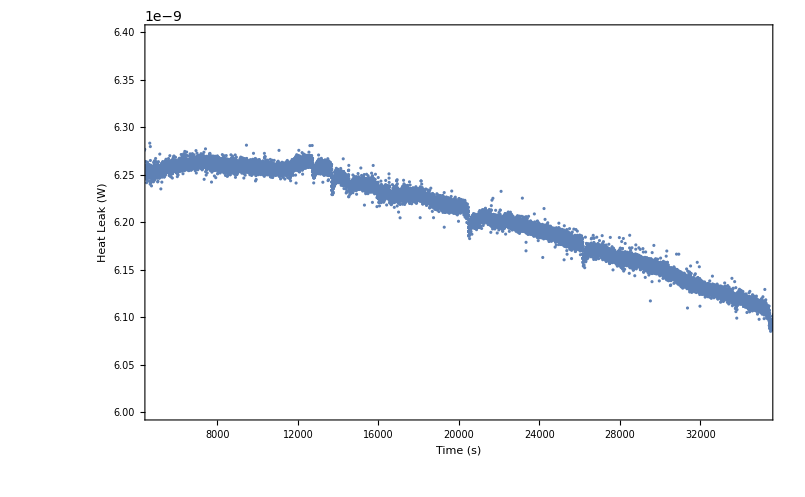

```mathematica
ListPlot[(CnuclearPR[1,dat1[[2;;,2]]])(tdot[dat1[[;;-2,1]]])/1000,Frame->True,FrameLabel->{"Time (s)","Heat Leak (W)"},BaseStyle->{Bold, FontSize->18},PlotRange->{{5000,35000},{6 10^-9,6.4 10^-9}}]
```

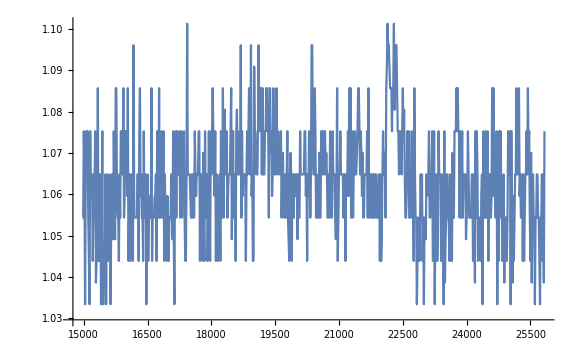

```mathematica
dat0=Import["finaldemag013116","Table"];
dat0[[2;;,4]]=dat0[[2;;,4]]-dat0[[2,4]];
ListPlot[dat0[[1000;;,{4,3}]],PlotRange->All,Joined->True]
```

```mathematica
dat0[[-10;;,3]]
```

{2.1602257788181305,2.1425239406526089,2.1602257788181305,2.1425239406526089,2.1425239406526089,2.1602257788181305,2.1070963740348816,2.1159562598913908,2.1026656832545996,2.1159562598913908}

```mathematica
Length[dat0]
```

56

```mathematica
Max[dat0[[2;;,4]]]
Min[dat0[[2;;,4]]]
```

3.537038786539×10^9

3.5370379765079999×10^9

{C(pF)\tPressure(bar)\tTemp(mK)\tTime(sec)\r\n1.81329999999999990000E+1,34.350983654064606,2.1319616129621863,3.5370379615079999×10^9}

```mathematica
(*Cryo 2 Initial Demag 08/19/2021*)
dat=Import["MCT_Demag3_210818","Table"];
```

```mathematica
dat[[2;;,4]]=dat[[2;;,4]]-dat[[2,4]];
```

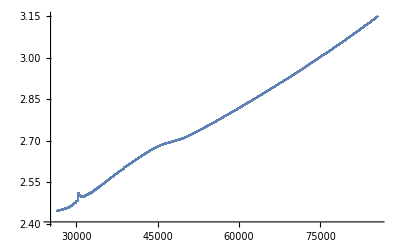

```mathematica
ListPlot[dat[[25000;;,{4,3}]]]
```

```mathematica
dat1=dat[[25000;;,{4,3}]];
```

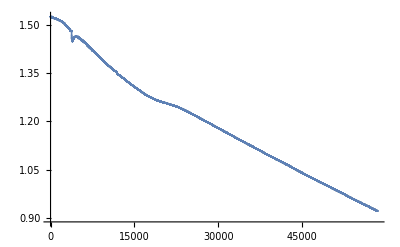

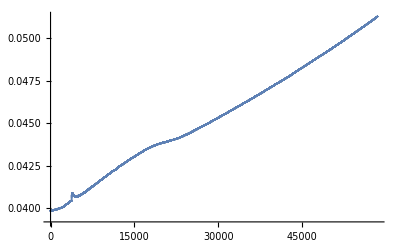

```mathematica
ListPlot[CnuclearPR[1,dat1[[;;,2]]]]
ListPlot[cvtot3He[dat1[[;;,2]],26.6,15]]
```

```mathematica
dat1[[1,1]]-dat1[[-1,1]]
dat1[[1,2]]-dat1[[-1,2]]
```

-59049.4127874

-0.7014772724360227

```mathematica
0.7/(1000 59000)*1.2
```

1.42373×10^-8

```mathematica
32/78.5*8
```

3.26115

```mathematica
(.015)^2*140*10^-6
```

3.15×10^-8

```mathematica
64./80
```

0.8

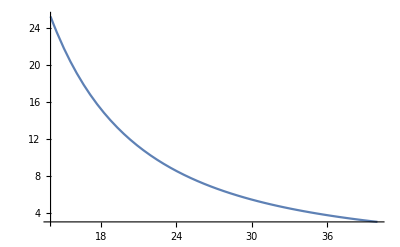

```mathematica
Plot[Cnuclear[68,t],{t,14,40}]
```

```mathematica
soln=NDSolve[{(7Cnuclear[68,temp[t]*1000]+25temp[t])temp'[t]+72(145 10^-6) temp[t]^2-1. 10^-6==0,temp[0]==0.10},temp[t],{t,0,350000}]

(*Plot[1000Evaluate[temp[t]/.soln],{t,0,300000},Frame->True,PlotRange->All,FrameLabel->{"Time (s)","Temp (mK)"},BaseStyle->{Bold,FontSize->20}]*)
```

{{temp[t]→InterpolatingFunction[…][t]}}

```mathematica
precool0801=Import["C:\\Users\\Man\\Dropbox\\Cooldown (MN)\\2020_07\\MCT_paro_PRECOOL_073120"];
```

```mathematica
precool0801[[2]]
```

{0.0059962272644042969,153.5850533246994,30.35315018751427,35.468229999999998,21.087389999999999,07/31/2020 18:30:39}

```mathematica
precool0801shift=precool0801;
precool0801shift[[All,1]]=precool0801[[All,1]];
```

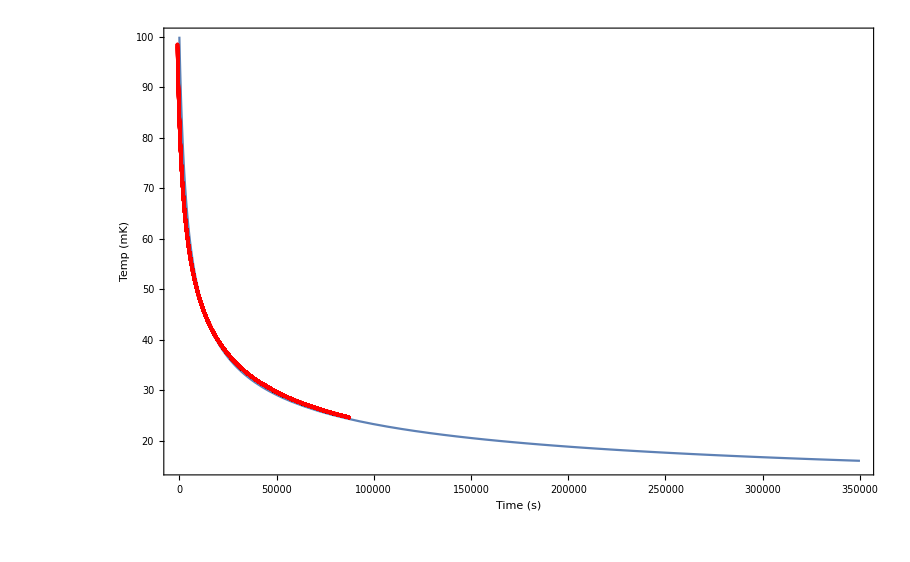

```mathematica
Show[{Plot[1000Evaluate[temp[t]/.soln],{t,0,350000},Frame->True,PlotRange->{All,{15,100}},FrameLabel->{"Time (s)","Temp (mK)"},BaseStyle->{Bold,FontSize->20}]
,
ListPlot[precool0801shift[[1000;;,1;;2]],PlotStyle->Red]
}]
```

```mathematica
300000/3600.
```

83.3333

```mathematica
Cnuclear[68,25]
25 0.025
cvtotMCT[25]
```

7.90649

0.625

0.0162772

```mathematica
3600*72
```

259200

```mathematica
84(145 10^-6) (8/1000.)^2
```

7.7952×10^-7

```mathematica
{{temp[t]->InterpolatingFunction[…][t]}}
Plot[%[[1]][[1]],{t,0,10000}]
```

{{temp[t]→InterpolatingFunction[…][t]}}

-Graphics-

```mathematica
Plot[temp[t],{t,0,10000}]
```

-Graphics-

```mathematica
4 .5 8.34
```

16.68

```mathematica
84 160 10^-6(8/1000.)^2
```

8.6016×10^-7

```mathematica
CnuclearPR[32,t]
cvtot3He[t,27,12]
cvtotMCT[70]
```

195164./t^2

3.52659 (0.00370781 t-3.49552×10^-7 t^3+3.29821×10^-9 t^4-1.03436×10^-11 t^5)

0.0303067

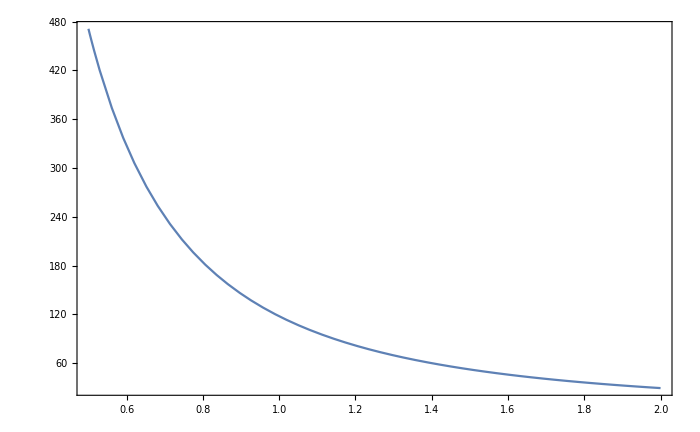

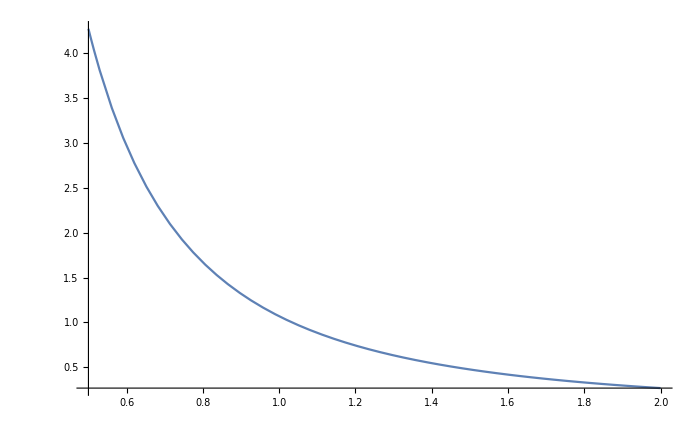

```mathematica
(*Table[CnuclearPR[i,t]+cvtot3He[t,30,14],{i,.02,.1,0.04}];*)
Plot[{CnuclearPR[1,t]},{t,.5,2},Frame->True,PlotRange->All]
Plot[{Cnuclear[1,t]},{t,0.5,2}]
```

```mathematica
(1.6 8/78.5)/2.6
(1. 8/78.5)/1.9
```

0.0627144

0.0536373

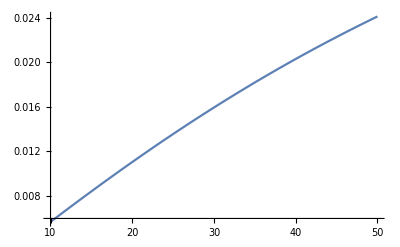

```mathematica
Plot[0.5/vmol[mctp[t]] 8.3cvfunc[vmol[mctp[t]],t],{t,10,50}]
```

```mathematica
(cvtotMCT[13.8]+cvtot3He[13.8,10,12])40 10^-6/3600(*Andrew heat leak at 13.8 mK with 10 bar in sample cell and 12 cc total volume in S.C., Tdot = 40 μK/hour converted to seconds*)
```

1.69042×10^-9

```mathematica
(cvtotMCT[17.5]+cvtot3He[17.5,1.56,12])((37 10^-6)/60)(*Tdot = 37 μK/min at 17.5 mK*)
(cvtotMCT[26.5]+cvtot3He[26.5,1.56,12])((27 10^-6)/60)(*Tdot = 27 μK/min at 26.5 mK*)
(*Cnuclear[65.5,13]*)
```

9.18671×10^-8

1.00299×10^-7

```mathematica
(500*10^-9)/(cvtotMCT[1]+cvtot3He[1,5,12]+Cnuclear[1,1])(* = ΔT (in K) from 500 nJ in energy at 1 mK, 5 bar and 12 cc in SC, and 1 Amp in NS*)
(*(cvtotMCT[26.5]+cvtot3He[26.5,1.56,12])*)
```

3.82223×10^-7

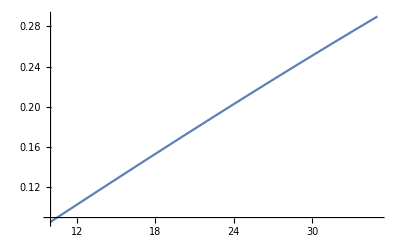

```mathematica
Plot[(cvtotMCT[t]+cvtot3He[t,1.56,12]),{t,10,35}]
```

```mathematica
8000*10^-6/(8.34 * 300)*1.75 10^5
```

0.559552

```mathematica
12/vmol[1.5]
```

0.339604

```mathematica
vmol[1.5]
```

35.3352

```mathematica
0.5/vmol[mctp[15]]
12/vmol[1.5]
```

0.0180414

0.339604

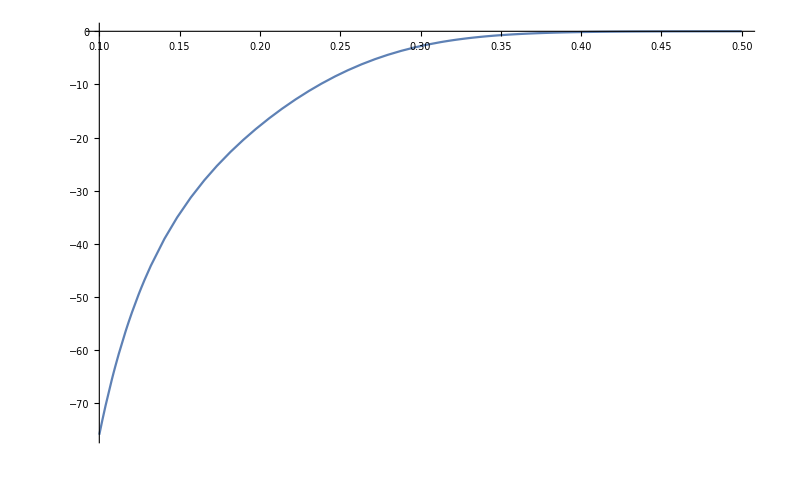

```mathematica
Plot[esym-ea,{a,.1,.5},PlotRange->All]
```

```mathematica
((125003-6250100 a^2) ⅇ^(-25 a^2) √π)/12500/.a->10//N
```

-1.62652320257207×10^-1081

```mathematica
vmol[p_]=Sum[vmolcoef[[i]] p^(i-1),{i,1,6}](*Molar volume as a function of pressure for 3He*);
.5/vmol[33.7]
4.4*% 8.34
```

0.0180309

0.661661

```mathematica
2.7*8.34
```

22.518

```mathematica
0.6/vmol[mctp[23]] 8.3
```

0.179468

```mathematica
cvtotMCT[22]/(.022)
```

0.548845

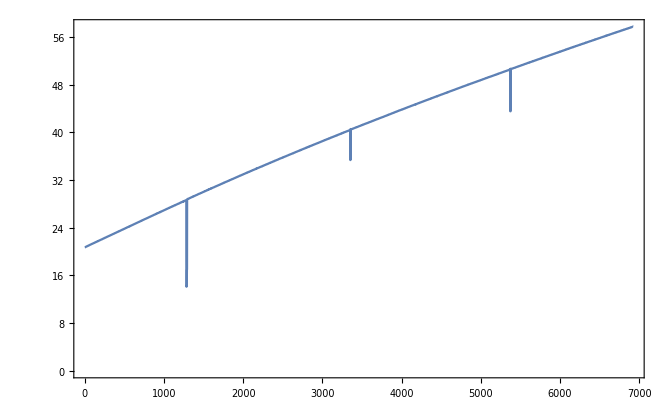

```mathematica
nsheatleak=Import["C:\\Users\\Man\\Desktop\\Cryo1_Man\\Cooldown (MN)\\2018_28_June\\(20180703) OneShot","Table"];
tmct=nsheatleak[[2;;,{1,2}]];
tmct=tmct[[-5300;;]];
tmct[[All,1]]=(tmct[[All,1]]-tmct[[1,1]])*60;
(*tmct=Drop[tmct,{745,751}];*)
ListLinePlot[tmct,Frame->True,PlotRange->All]
```

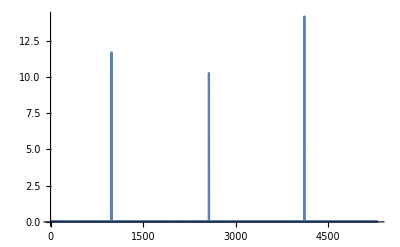

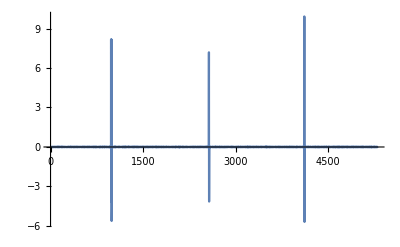

{{981},{982},{983},{987},{988},{989},{2566},{2567},{2568},{4112},{4113},{4114}}

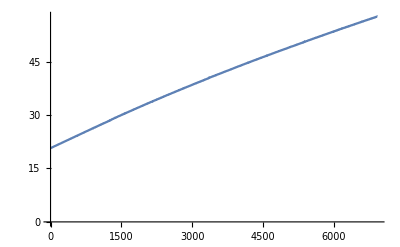

```mathematica
diff=Abs@Differences[tmct[[All,2]],2];

ListPlot[diff,PlotRange->All,Joined->True]

movavg=ArrayPad[MovingAverage[diff,5],{4,0},"Fixed"];
submean=Subtract@@@Transpose[{diff,movavg}];
ListLinePlot[%,PlotRange->All]
outpos=Position[submean,x_/;x>StandardDeviation[submean]*1]
newtmct=Delete[tmct,outpos];
newtmct=Delete[newtmct,{{981},{982},{983}}];
ListLinePlot[{%},PlotRange->All]
```

{{984}}

{{1283.09,18.4144},{1284.4,14.1066},{1285.71,14.2743},{1287.02,14.2858},{1288.32,14.2904},{1289.63,16.8675},{1290.94,17.0771}}

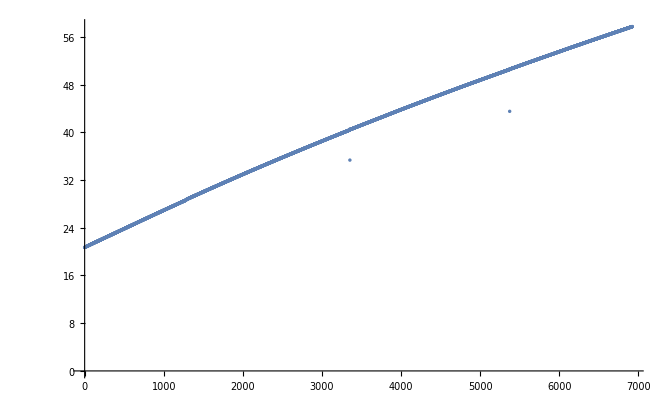

```mathematica
Position[tmct[[All,2]],Min[tmct[[All,2]]]]
tmct[[983;;989]]
tmct=Drop[tmct,{983,989}];
ListPlot[tmct]
```

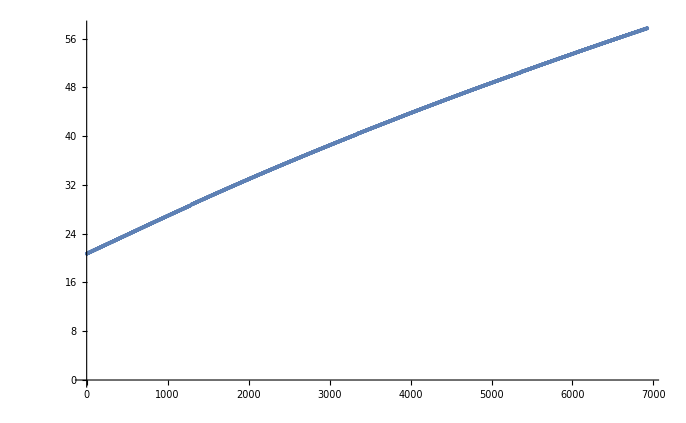

```mathematica
Show[
ListPlot[newtmct]
,Plot[polyfit,{x,0,2000},PlotStyle->Red]
]
```

```mathematica
cvtotMCT[tmct[[1,2]]]tmct[[1,2]]
```

0.254141

```mathematica
polyfit=Fit[newtmct,{1,x,x^2,x^3,x^4},x]
D[polyfit,x]
```

20.6549+0.00647194 x-1.60716×10^-7 x^2-6.74431×10^-12 x^3+9.59022×10^-16 x^4

0.00647194-3.21432×10^-7 x-2.02329×10^-11 x^2+3.83609×10^-15 x^3

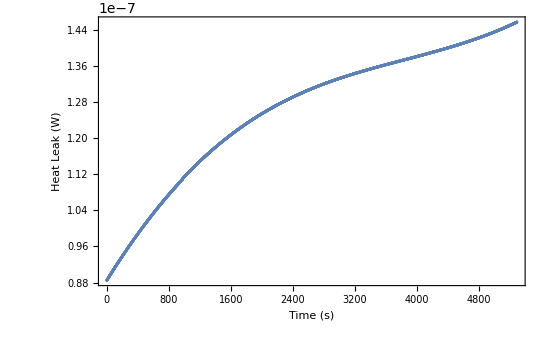

```mathematica
ListPlot[(1/1000 D[polyfit,x])cvtotMCT[polyfit]/.x->newtmct[[All,1]],Frame->True,PlotRange->All,BaseStyle->FontSize->18,FrameLabel->{"Time (s)","Heat Leak (W)"}]
```

```mathematica
((140 10^-6)3600 43.)22.4
```

485.453

```mathematica
(.609166-.794029)/(.0001/.00012)
```

-0.221836

```mathematica
36.82/22
22/27.5
```

1.67364

0.8